```mathematica
Phi=Symbol["Phi"];
Theta=Symbol["Theta"];

Rot={Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]};

Theta = Pi/2;
Phi=Pi/3;
module = Sqrt[(Sin[Phi]*Cos[Theta])^2 + (Sin[Phi]*Sin[Theta])^2+Cos[Phi]^2]
```

1

```mathematica
Manipulate[Graphics3D[{{Opacity[0.3],Sphere[{0,0,0},1]},Arrow[{{0,0,0},{Sin[Phi]*Cos[Theta],Sin[Phi]*Sin[Theta],Cos[Phi]}}] },PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->True,AxesLabel->{"X","Y","Z"},LabelStyle->Directive[Bold,12],ImageSize->Large ],{{Phi,Pi,"Phi"},0,Pi,Pi/100},{{Theta,Pi,"Theta"},0,2 Pi,Pi/100} ]
```

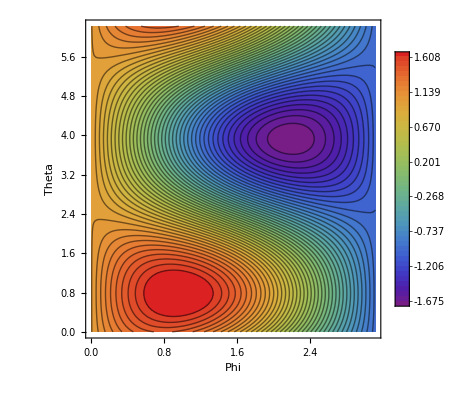

```mathematica
numPoints=100;
phi=Subdivide[0,Pi,numPoints];
theta=Subdivide[0,2 Pi,numPoints];

SingSpinEnergy=Table[S={Sin[phi[[i]]] Cos[theta[[j]]],Sin[phi[[i]]] Sin[theta[[j]]],Cos[phi[[i]]]};
energy=Total[S];
{phi[[i]],theta[[j]],energy},{i,1,numPoints},{j,1,numPoints}];

flatList=Flatten[SingSpinEnergy,1];


ListContourPlot[flatList,Contours->50,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Phi","Theta"},PlotRange->All]
```